## Taylor and Implicit programs

```mathematica
Off[General::spell]
Off[General::spell1]

Taylor[f_,x_,x0_,r_]:=
Module[{n,mp,v1,vu,c,g,hg,l,fac,pr,dein,ap,de,sostfi(*,tay*)},
n=Length[x];
mp=Join[Table[in[i],{i,1,n}],{0}];
v1=Table[{mp[[i]]-mp[[i+1]]},{i,1,n}]//Flatten;
vu=Table[{mp[[i]],0,c[i]},{i,1,n}];
c[1]=r;
c[i_]:=mp[[i-1]]/;i>1;
g[w1_,{z1__}]:=Flatten[Table[w1,z1],n-1];
hg=g[v1,vu];
l=Length[hg];
fac[i_]:=Product[
Factorial[hg[[i,j]]],
{j,1,Length[hg[[i]]]}];
pr[i_]:=Product[(x[[j]]-x0[[j]])^hg[[i,j]],{j,1,n}];
dein[i_]:=Table[{x[[j]],hg[[i,j]]},{j,1,n}];
ap[{q__}]:=q;
de[i_]:=D[f,ap[dein[i]]];
sostfi=Table[x[[i]]->x0[[i]],{i,1,n}];
tay=Sum[(1/fac[i])*(de[i]/.sostfi)*pr[i],{i,1,l}]

]

Off[General::spell];
Off[General::spell1];

Implicit[sys_,inc_,var_,inc0_,var0_,r_]:=Module[{pininc,pinvar,pin,ap,u,in,sist,m,sol,unk,num,dersys},n1=Length[inc];
n2=Length[var];
(*Calcolo della matrice jacobiana nel punto iniziale*)
pininc=Table[inc[[h]]->inc0[[h]],{h,1,n1}];
pinvar=Table[var[[h]]->var0[[h]],{h,1,n2}];
pin=Join[pininc,pinvar];
coeff[h_,k_]:=D[sys[[h]],inc[[k]]];
Jac=Det[Table[coeff[h,k],{h,1,n1},{k,1,n1}]/.pin]//Simplify;
Print["J = ",Jac];
(*Occorre definire le incognite come funzioni u=Table[fu[var]] delle variabili var;u0 è la tabella di queste funzioni in var0;sist è il sistema di queste funzioni*)
ap[fu_,{q__}]:=fu[q];
u=Table[ap[fu[h],var],{h,1,n1}];
u0=Table[ap[fu[h],var0],{h,1,n1}];
in=Table[inc[[h]]->u[[h]],{h,1,n1}];
sist=Flatten[Table[sys[[h]]/.in,{h,1,n1}]];
mu=Flatten[Join[Table[u0[[h]]->inc0[[h]],{h,1,n1}],Table[var[[h]]->var0[[h]],{h,1,n2}]]];
(*Calcolo delle derivate delle funzioni sys rispetto alle variabili indipendenti var*)
sol[0]=mu;
unk[0]=inc0;
Do[dersys[0]=sist;
num[0]=n1;
num[j]=n2*num[j-1];
dersys[j]=Flatten[Table[D[dersys[j-1],var[[i]]],{i,1,n2}]],{j,1,r}];
(*Calcolo delle derivate delle funzioni inc riguardate come funzioni delle variabili var*)
Do[derinc[0]=u;
derinc[j]=Flatten[Table[D[derinc[j-1],var[[i]]],{i,1,n2}]];
der0[j]=derinc[j]/.Table[Flatten[var[[i]]->var0[[i]]],{i,1,n2}],{j,1,r}];
Do[m1[j]=Flatten[Table[sol[h],{h,0,j-1}]];
sol[j]=Flatten[Solve[(dersys[j]//.m1[j])==0,der0[j]]],{j,1,r}];
(*Uso delle derivate fino all'ordine r rispetto a tutte le variabili contenute in sol[j] da 1 a r*)
apq[{q__}]:=q;
apr[x_,{q__}]:=D[x,q];
(*Il numero massimo di variabili indipendenti è 6*)ta={{q[1],a1_},{q[2],a2_},{q[3],a3_},{q[4],a4_},{q[5],a5_},{q[6],a6_}};
pr={a1,a2,a3,a4,a5,a6};
rs=Table[q[i]->var[[i]],{i,1,n2}];
tan=Table[ta[[i]]/.rs,{i,1,n2}];
prn=Table[pr[[i]],{i,1,n2}];
co[h_]:=apr[fu[h][apq[var]],tan];
co0[h_]:=co[h]/.Flatten[Table[var[[i]]->var0[[i]],{i,1,n2}]];
(*Riordinamento della soluzione sol[j]*)t1[j_]:=Table[{sol[j][[k,1]],sol[j][[k,2]]},{k,1,Length[sol[j]]}];
solrid[h_,j_]:=Cases[t1[j],{co0[h],x_}];
solrid1[h_,j_]:=Table[solrid[h,j][[k,1]],{k,1,Length[solrid[h,j]]}];
solrid2[h_,j_]:=Table[solrid[h,j][[k,2]],{k,1,Length[solrid[h,j]]}];
pot[h_,j_]:=Cases[solrid1[h,j],co0[h]->prn];
esp[h_,j_,k_,i_]:=pot[h,j][[k,i]];
(*Sviluppo di Taylor delle funzioni incognite*)s[h_,j_]:=Sum[solrid2[h,j][[k]]*Product[(1/esp[h,j,k,i]!)*var[[i]]^esp[h,j,k,i],{i,1,n2}],{k,1,Length[solrid[h,j]]}];
tayl[h_]:=inc0[[h]]+Sum[s[h,j],{j,1,r}];
(*Do[Print[inc[[h]]," = ",tayl[h]],{h,1,n1}]*)
]
```

```mathematica
(*aa = Sin[y1] - x; 
bb = Log[y2] - x; 
Implicit[{aa, bb}, {y1, y2}, {x}, {0, 1}, {0}, 5]*)
```

```mathematica
Taylor[ArcCos[x],{x},{0},5]
```

π/2-x-x^3/6-(3 x^5)/40

```mathematica
Taylor[(R-√(R^2-(1+K)ρ^2))/(1+K),{ρ},{0},6]
```

(R-√(R^2))/(1+K)+ρ^2/(2 √(R^2))+((1+K) ρ^4)/(8 (R^2)^(3/2))+((1+K)^2 ρ^6)/(16 (R^2)^(5/2))

## Third-order expansion of the equation of Gaussian surface Σ_g

The implicit equation of Σ_g in the Cartesian frame with the origin at the exit pupil,is

```mathematica
eq=(Subscript[X, g])^2+(Subscript[Y, g]-M Subscript[y, 1])^2+(Subscript[Z, g]-SubStar[z])^2-SubStar[z]^2-M^2 Subscript[y, 1]^2 (*=0*); (* z_*=Subscript[z, n]'-Subscript[w, n]' *)
```

since Σ_g has the center at  (0, My_1, z_*) and radius √((z_*)^2+M^2 y_1^2). The third - order expansion of the function Z_g(X_g,Y_g,y_1) , that is implicitly defined by the above equation, is

```mathematica
Implicit[{eq},{Subscript[Z, g]},{Subscript[X, g],Subscript[Y, g],Subscript[y, 1]},{0},{0,0,0},3]
tayl[1]
```

J = -2 z_*

X_g^2/(2 z_*)-(M y_1 Y_g)/(z_*)+Y_g^2/(2 z_*)

The implicit equation of Σ_g in the Cartesian frame with the origin at the exit pupil,is

```mathematica
Subscript[Z, g]=(Subscript[X, g]^2+Subscript[Y, g]^2)/(2 SubStar[z])-(M Subscript[y, 1] Subscript[Y, g])/SubStar[z];
```

## Intersection point of the third-order ray with Σ_g. Evaluation of the functions Xg(xe,ye,y )and Y_g(xe,ye,y) up to third-order

Aberration formulae for the image plane and exit pupil.  (α=1/(w1-z1))

```mathematica
ϵx=SubStar[z]/(Nn1 Subscript[M, e])(4 Subscript[D, 1](xe^2+ye^2)xe-2α Subscript[D, 2] xe ye y +2 α^2 Subscript[D, 3] xe y^2);
ϵy=SubStar[z]/(Nn1 Subscript[M, e])(4 Subscript[D, 1](xe^2+ye^2)ye-α Subscript[D, 2](xe^2+3 ye^2) y +2 α^2 Subscript[D, 4] ye y^2-α^3 Subscript[D, 5] y^3);
ϵex=-SubStar[z]/(Nn1 M)(α Subscript[De, 2] xe y^2+2 α^2(Subscript[De, 4]-Subscript[De, 3]) xe y ye+α^3 Subscript[De, 5] xe (xe^2+ye^2));
ϵey=-SubStar[z]/(Nn1 M)(4 Subscript[De, 1] y^3+3α Subscript[De, 2] y^2 ye +2 α^2 y (Subscript[De, 3] xe^2+Subscript[De, 4] ye^2)+α^3 Subscript[De, 5] ye (xe^2+ye^2));
```

We consider the parametric equations of the  ray between the points (Me xe+ϵex,Me ye+ϵey,0) and  (ϵ_x,M y_1+ϵ_y, z_*).

```mathematica
X=Me xe +ϵex+(ϵx-Me xe-ϵex)t;    (*t∈[0,1} *)
Y=Me ye+ϵey+(M y +ϵy-Me ye-ϵey)t;
Z=SubStar[z] t;
```

We first determine the value of the parameter t corresponding to the intersection point of the ray with Σ_g .

```mathematica
eq1=SubStar[z] t-(X^2+Y^2)/(2 SubStar[z])+(M y Y)/SubStar[z];
```

```mathematica
Implicit[{eq1},{t},{xe,ye,y},{0},{0,0,0},3];
t1=tayl[1]
```

J = z_*

(Me^2 xe^2)/(2 z_*^2)-(M Me y ye)/(z_*^2)+(Me^2 ye^2)/(2 z_*^2)

```mathematica
Xg=X//.t->t1;
Yg=Y/.t->t1;
Zg=Z/.t->t1;
```

Coordinates of  the intersection point of the ray with Σ_g .

```mathematica
TApp=Taylor[{Xg,Yg,Zg},{xe,ye,y},{0,0,0},3]
```

{Me xe-(xe y^2 α De_2 z_*)/(M Nn1)+xe y ye ((M Me^2)/(z_*^2)-(2 α^2 (-De_3+De_4) z_*)/(M Nn1))+1/6 xe^3 (-(3 Me^3)/(z_*^2)-(6 α^3 De_5 z_*)/(M Nn1))+1/2 xe ye^2 (-Me^3/(z_*^2)-(2 α^3 De_5 z_*)/(M Nn1)),Me ye-(4 y^3 De_1 z_*)/(M Nn1)+1/2 y^2 ye (-(2 M^2 Me)/(z_*^2)-(6 α De_2 z_*)/(M Nn1))+1/2 xe^2 y ((M Me^2)/(z_*^2)-(4 α^2 De_3 z_*)/(M Nn1))+1/2 y ye^2 ((3 M Me^2)/(z_*^2)-(4 α^2 De_4 z_*)/(M Nn1))+1/6 ye^3 (-(3 Me^3)/(z_*^2)-(6 α^3 De_5 z_*)/(M Nn1))+1/2 xe^2 ye (-Me^3/(z_*^2)-(2 α^3 De_5 z_*)/(M Nn1)),(Me^2 xe^2)/(2 z_*)-(M Me y ye)/(z_*)+(Me^2 ye^2)/(2 z_*)}

```mathematica
eqXg=Subscript[X, g]-(Me xe-(xe y^2 α Subscript[De, 2] SubStar[z])/(M Nn1)+xe y ye ((M Me^2)/SubStar[z]^2-(2 α^2 (-Subscript[De, 3]+Subscript[De, 4]) SubStar[z])/(M Nn1))+1/6 xe^3 (-(3 Me^3)/SubStar[z]^2-(6 α^3 Subscript[De, 5] SubStar[z])/(M Nn1))+1/2 xe ye^2 (-Me^3/SubStar[z]^2-(2 α^3 Subscript[De, 5] SubStar[z])/(M Nn1)));
eqYg=Subscript[Y, g]-(Me ye-(4 y^3 Subscript[De, 1] SubStar[z])/(M Nn1)+1/2 y^2 ye (-(2 M^2 Me)/SubStar[z]^2-(6 α Subscript[De, 2] SubStar[z])/(M Nn1))+1/2 xe^2 y ((M Me^2)/SubStar[z]^2-(4 α^2 Subscript[De, 3] SubStar[z])/(M Nn1))+1/2 y ye^2 ((3 M Me^2)/SubStar[z]^2-(4 α^2 Subscript[De, 4] SubStar[z])/(M Nn1))+1/6 ye^3 (-(3 Me^3)/SubStar[z]^2-(6 α^3 Subscript[De, 5] SubStar[z])/(M Nn1))+1/2 xe^2 ye (-Me^3/SubStar[z]^2-(2 α^3 Subscript[De, 5] SubStar[z])/(M Nn1)));
eqZg=Subscript[Z, g]-((Me^2 xe^2)/(2 SubStar[z])-(M Me y ye)/SubStar[z]+(Me^2 ye^2)/(2 SubStar[z]));
Implicit[{eqXg,eqYg},{xe,ye},{y,Subscript[X, g],Subscript[Y, g]},{0,0},{0,0,0},3]
```

J = Me^2

```mathematica
tayl[1]
tayl[2]
```

X_g/Me+(y^2 α De_2 X_g z_*)/(M Me^2 Nn1)+(y X_g Y_g (-M^2 Me^2 Nn1-2 α^2 De_3 z_*^3+2 α^2 De_4 z_*^3))/(M Me^3 Nn1 z_*^2)+(X_g^3 (M Me^3 Nn1+2 α^3 De_5 z_*^3))/(2 M Me^4 Nn1 z_*^2)+(X_g Y_g^2 (M Me^3 Nn1+2 α^3 De_5 z_*^3))/(2 M Me^4 Nn1 z_*^2)

Y_g/Me+(4 y^3 De_1 z_*)/(M Me Nn1)+(y^2 Y_g (M^3 Me Nn1+3 α De_2 z_*^3))/(M Me^2 Nn1 z_*^2)+(y X_g^2 (-M^2 Me^2 Nn1+4 α^2 De_3 z_*^3))/(2 M Me^3 Nn1 z_*^2)+(y Y_g^2 (-3 M^2 Me^2 Nn1+4 α^2 De_4 z_*^3))/(2 M Me^3 Nn1 z_*^2)+(X_g^2 Y_g (M Me^3 Nn1+2 α^3 De_5 z_*^3))/(2 M Me^4 Nn1 z_*^2)+(Y_g^3 (M Me^3 Nn1+2 α^3 De_5 z_*^3))/(2 M Me^4 Nn1 z_*^2)

```mathematica
(M Me^2)/SubStar[z]^2+(2 α^2 (Subscript[De, 3]-Subscript[De, 4]) SubStar[z])/(M Nn1)
```

## Third-order and fifth-order aberration vectors

W(η,ζ,ξ) is the optical difference path and η= X^2+Y^2, ζ=Y y, ξ = y^2 . The first-order Taylor expansion corresponds to the Gaussian optics.

```mathematica
aaa=Taylor[W[η,ζ,ξ],{η,ζ,ξ},{0,0,0},2]-Taylor[W[η,ζ,ξ],{η,ζ,ξ},{0,0,0},1]
```

1/2 ξ^2 W^(0,0,2)[0,0,0]+ζ ξ W^(0,1,1)[0,0,0]+1/2 ζ^2 W^(0,2,0)[0,0,0]+η ξ W^(1,0,1)[0,0,0]+ζ η W^(1,1,0)[0,0,0]+1/2 η^2 W^(2,0,0)[0,0,0]

```mathematica
W3[η,ζ,ξ]=1/2 η ξ^2 Derivative[1,0,2][W][0,0,0]+ζ η ξ Derivative[1,1,1][W][0,0,0]+1/2 ζ^2 η Derivative[1,2,0][W][0,0,0]+1/2 η^2 ξ Derivative[2,0,1][W][0,0,0]+1/2 ζ η^2 Derivative[2,1,0][W][0,0,0]+1/6 η^3 Derivative[3,0,0][W][0,0,0]+1/6 ξ^3 Derivative[0,0,3][W][0,0,0]+1/2 ζ ξ^2 Derivative[0,1,2][W][0,0,0]+1/2 ζ^2 ξ Derivative[0,2,1][W][0,0,0]+1/6 ζ^3 Derivative[0,3,0][W][0,0,0];
```

```mathematica
W2[η,ζ,ξ]=aaa/.{η->X^2+Y^2,ζ->y Y,ξ->y^2}
```

```mathematica
y^4 D6+y^3 Y D5+D4 y^2 Y^2 +D3 y^2 (X^2+Y^2) +D2 y Y (X^2+Y^2) +D1 (X^2+Y^2)^2
```

```mathematica
W2=D1 η^2 +D2 η ζ+D3 η ξ +D4 ζ^2 +D5 ζ ξ +D6 ξ^2 ;
W3=B1 η^3 +B2 ζ η^2 +B3 ζ^2 η +B4 η^2 ξ +B5 ζ η ξ +B6 ζ^3 +B7 ζ^2 ξ +B8 η ξ^2 +B9 ζ ξ^2 +B10 ξ^3 ;
```

```mathematica
W22=W2/.{η->X^2+Y^2,ζ->y Y,ξ->y^2}
W33=W3/.{η->X^2+Y^2,ζ->y Y,ξ->y^2}
```

D6 y^4+D5 y^3 Y+D4 y^2 Y^2+D3 y^2 (X^2+Y^2)+D2 y Y (X^2+Y^2)+D1 (X^2+Y^2)^2

B10 y^6+B9 y^5 Y+B7 y^4 Y^2+B6 y^3 Y^3+B8 y^4 (X^2+Y^2)+B5 y^3 Y (X^2+Y^2)+B3 y^2 Y^2 (X^2+Y^2)+B4 y^2 (X^2+Y^2)^2+B2 y Y (X^2+Y^2)^2+B1 (X^2+Y^2)^3

```mathematica
(* calculations *)
(*
D4 y^2 Y^2+D3 y^2 (X^2+Y^2)=y^2(D4 Y^2+D3 X^2+D3 Y^2)=y^2(D3 X^2+(D4+D3)Y^2); (* We call D4+D3=D4 *)
B3 y^2 Y^2 (X^2+Y^2)+B4 y^2 (X^2+Y^2)^2=y^2(X^2+Y^2)(B3 Y^2+B4(X^2+Y^2))=y^2(X^2+Y^2)(B4 X^2+(B3+B4)Y^2)(* We call B4+B3=B3 *)
*)
```

```mathematica
(* the above formulae written ordering by the indices of Subscript[D, i] and Subscript[B, i]*)
(*
W222=D1 (X^2+Y^2)^2+D2 y Y (X^2+Y^2)+(D4 Y^2+D3  X^2)y^2+D5 y^3 Y+D6 y^4; (* We put B4+B3=B4 *)
W333=B1 (X^2+Y^2)^3+B2 y Y (X^2+Y^2)^2+y^2(X^2+Y^2)(B4 X^2+B3 Y^2)+B5 y^3 Y (X^2+Y^2)+B6 y^3 Y^3+B7 y^4 Y^2+B8 y^4 (X^2+Y^2)+B9 y^5 Y+B10 y^6;
*)
```

```mathematica
ϵx3= D[W22,X]
ϵy3= D[W22,Y]
```

2 D3 X y^2+2 D2 X y Y+4 D1 X (X^2+Y^2)

D5 y^3+2 D3 y^2 Y+2 D4 y^2 Y+2 D2 y Y^2+D2 y (X^2+Y^2)+4 D1 Y (X^2+Y^2)

```mathematica
(* calculations *)
2 D2 y Y^2+D2 y (X^2+Y^2)=D2 y(2 Y^2+X^2+Y^2)=D2 y(X^2+3 Y^2)
```

```mathematica
ϵx3= (4 D1 (X^2+Y^2)X+2 D2 X Y y+2 D3 X y^2);
```

```mathematica
ϵy3= (4 D1 (X^2+Y^2)Y+D2 y (X^2+3 Y^2)+2  D4 y^2 Y+D5 y^3);
```

```mathematica
ϵx3p=(ϵx3/.{X->r Sin[ϕ],Y->r Cos[ϕ]})//TrigReduce
ϵy3p=ϵy3/.{X->r Sin[ϕ],Y->r Cos[ϕ]}//TrigReduce
```

4 D1 r^3 Sin[ϕ]+2 D3 r y^2 Sin[ϕ]+D2 r^2 y Sin[2 ϕ]

2 D2 r^2 y+D5 y^3+4 D1 r^3 Cos[ϕ]+2 D4 r y^2 Cos[ϕ]+D2 r^2 y Cos[2 ϕ]

```mathematica
(* calculations *)
2 D2 r^2 y+D2 r^2 y Cos[2 ϕ]=D2 r^2 y(2+Cos[2ϕ])
```

```mathematica
ϵxpol= a(4 D1 r^3 Sin[ϕ]+D2 r^2 y Sin[2 ϕ]+2 D3 r y^2 Sin[ϕ]);
ϵxpol= a(4 D1 r^3 Cos[ϕ]+D2 (2+Cos[2 ϕ])r^2 y +2D4 r y^2 Cos[ϕ]+D5 y^3);
```

```mathematica
Cos[θ]=Cos[(π/2-ϕ)]=Sin[ϕ];
Sin[θ]=Sin[(π/2-ϕ)]=Cos[ϕ];
Cos[2 θ]=Cos[2 (π/2-ϕ)]=-Cos[2 ϕ];
Sin[2 θ]=Sin[2 (π/2-ϕ)]=Sin[2 ϕ];
```

```mathematica
ϵx5= D[W33,X]
ϵy5= D[W33,Y]
```

2 B8 X y^4+2 B5 X y^3 Y+2 B3 X y^2 Y^2+4 B4 X y^2 (X^2+Y^2)+4 B2 X y Y (X^2+Y^2)+6 B1 X (X^2+Y^2)^2

B9 y^5+2 B7 y^4 Y+2 B8 y^4 Y+2 B5 y^3 Y^2+3 B6 y^3 Y^2+2 B3 y^2 Y^3+B5 y^3 (X^2+Y^2)+2 B3 y^2 Y (X^2+Y^2)+4 B4 y^2 Y (X^2+Y^2)+4 B2 y Y^2 (X^2+Y^2)+B2 y (X^2+Y^2)^2+6 B1 Y (X^2+Y^2)^2

```mathematica
(*Simplifications *)
4 B2 y Y^2 (X^2+Y^2)+B2 y (X^2+Y^2)^2=B2 y (X^2+Y^2)(4 Y^2+X^2+Y^2)=B2 y (X^2+Y^2)(X^2+5 Y^2)
B5 y^3 (X^2+Y^2)+2 B5 y^3 Y^2=B5 y^3(X^2+Y^2+2 Y^2)=B5 y^3(X^2+3 Y^2)
```

```mathematica
ϵ5x=(ϵx5/.{X->r Sin[ϕ],Y->r Cos[ϕ]})//TrigReduce
```

1/2 (12 B1 r^5 Sin[ϕ]+B3 r^3 y^2 Sin[ϕ]+8 B4 r^3 y^2 Sin[ϕ]+4 B8 r y^4 Sin[ϕ]+4 B2 r^4 y Sin[2 ϕ]+2 B5 r^2 y^3 Sin[2 ϕ]+B3 r^3 y^2 Sin[3 ϕ])

```mathematica
Coefficient[ϵ5x,r^5]
```

6 B1 Sin[ϕ]

```mathematica
Coefficient[ϵ5x,r^4 y]//Simplify
```

2 B2 Sin[2 ϕ]

```mathematica
Coefficient[ϵ5x,r^3 y^2]//TrigReduce
```

1/2 (B3 Sin[ϕ]+8 B4 Sin[ϕ]+B3 Sin[3 ϕ])

```mathematica
(*Calculations*)
1/2 (B3 Sin[ϕ]+8 B4 Sin[ϕ]+B3 Sin[3 ϕ])=1/2 (B3 Sin[ϕ]+8 B4 Sin[ϕ]+B3 (3 Cos[ϕ]^2 Sin[ϕ]-Sin[ϕ]^3))=1/2 Sin[ϕ](B3 +8 B4+B3 (3 Cos[ϕ]^2 -Sin[ϕ]^2))=1/2 Sin[ϕ](B3 +8 B4+B3 (3 Cos[ϕ]^2 -1+Cos[ϕ]^2))=1/2 Sin[ϕ](8 B4-2B3+4B3 Cos[ϕ]^2 )=Sin[ϕ](4B4-B3+2B3 Cos[ϕ]^2 )
```

```mathematica
Coefficient[ϵ5x,r^2 y^3]//TrigReduce
```

B5 Sin[2 ϕ]

```mathematica
Coefficient[ϵ5x,r y^4]//TrigReduce
```

2 B8 Sin[ϕ]

```mathematica
Coefficient[ϵ5x,y^5]//TrigReduce
```

0

```mathematica
ϵ5y=((ϵy5)/.{X->r Sin[ϕ],Y->r Cos[ϕ]})//TrigReduce
```

1/2 (6 B2 r^4 y+4 B5 r^2 y^3+3 B6 r^2 y^3+2 B9 y^5+12 B1 r^5 Cos[ϕ]+7 B3 r^3 y^2 Cos[ϕ]+8 B4 r^3 y^2 Cos[ϕ]+4 B7 r y^4 Cos[ϕ]+4 B8 r y^4 Cos[ϕ]+4 B2 r^4 y Cos[2 ϕ]+2 B5 r^2 y^3 Cos[2 ϕ]+3 B6 r^2 y^3 Cos[2 ϕ]+B3 r^3 y^2 Cos[3 ϕ])

```mathematica
Coefficient[ϵ5y,r^5]
```

6 B1 Cos[ϕ]

```mathematica
Coefficient[ϵ5y,r^4 y]//Simplify
```

B2 (3+2 Cos[2 ϕ])

```mathematica
Coefficient[ϵ5y,r^3 y^2]//TrigReduce
```

1/2 (7 B3 Cos[ϕ]+8 B4 Cos[ϕ]+B3 Cos[3 ϕ])

```mathematica
(* Calculations *)
(* First fom *)
 (7/2 B3 Cos[ϕ]+4 B4 )Cos[ϕ]+1/2 B3 Cos[3 ϕ]
(* Second fom *)
1/2 (7 B3 Cos[ϕ]+8 B4 Cos[ϕ]+B3 Cos[3 ϕ])=1/2 (7 B3 Cos[ϕ]+8 B4 Cos[ϕ]+B3 (Cos[ϕ]^3-3 Cos[ϕ] Sin[ϕ]^2))=1/2 (7 B3 +8 B4 +B3 (Cos[ϕ]^2-3  Sin[ϕ]^2))Cos[ϕ]=1/2 (7 B3 +8 B4 +B3 (4 Cos[ϕ]^2-3  ))Cos[ϕ]=1/2 (4 B3 +8 B4 +B3 4 Cos[ϕ]^2 )Cos[ϕ]= (4 B4 +2B3 (1+Cos[ϕ]^2 ) )Cos[ϕ]
```

```mathematica
Coefficient[ϵ5y,r^2 y^3]//TrigReduce
```

1/2 (4 B5+3 B6+2 B5 Cos[2 ϕ]+3 B6 Cos[2 ϕ])

```mathematica
(* Calculations *)
1/2 (4 B5+3 B6+2 B5 Cos[2 ϕ]+3 B6 Cos[2 ϕ])= (2 B5+3/2 B6+(B5 +3/2 B6) Cos[2 ϕ]);
```

```mathematica
Coefficient[ϵ5y,r y^4]//TrigReduce
```

2 (B7 Cos[ϕ]+B8 Cos[ϕ])

```mathematica
2 (B7 Cos[ϕ]+B8 Cos[ϕ])=2 (B7 +B8 )Cos[ϕ]
```

```mathematica
Coefficient[ϵ5y,y^5]//TrigReduce
```

B9

```mathematica
1/2 (12 B1 r^5 Sin[ϕ]+B3 r^3 y^2 Sin[ϕ]+8 B4 r^3 y^2 Sin[ϕ]+4 B8 r y^4 Sin[ϕ]+4 B2 r^4 y Sin[2 ϕ]+2 B5 r^2 y^3 Sin[2 ϕ]+B3 r^3 y^2 Sin[3 ϕ])
1/2 (6 B2 r^4 y+4 B5 r^2 y^3+3 B6 r^2 y^3+2 B9 y^5+12 B1 r^5 Cos[ϕ]+7 B3 r^3 y^2 Cos[ϕ]+8 B4 r^3 y^2 Cos[ϕ]+4 B7 r y^4 Cos[ϕ]+4 B8 r y^4 Cos[ϕ]+4 B2 r^4 y Cos[2 ϕ]+2 B5 r^2 y^3 Cos[2 ϕ]+3 B6 r^2 y^3 Cos[2 ϕ]+B3 r^3 y^2 Cos[3 ϕ])
```

```mathematica
1/2 (12 B1 r^5 Sin[ϕ]+4 B8 r y^4 Sin[ϕ]+((B3+8B4) Sin[ϕ]+B3 Sin[3 ϕ])r^3 y^2 +4 B2 r^4 y Sin[2 ϕ]+2 B5 r^2 y^3 Sin[2 ϕ])

1/2 (12 B1 r^5 Cos[ϕ]+6 B2 r^4 y+4 B2 r^4 y Cos[2 ϕ]+4 B5 r^2 y^3+3 B6 r^2 y^3+7 B3 r^3 y^2 Cos[ϕ]+8 B4 r^3 y^2 Cos[ϕ]+4 B7 r y^4 Cos[ϕ]+4 B8 r y^4 Cos[ϕ]+2 B5 r^2 y^3 Cos[2 ϕ]+3 B6 r^2 y^3 Cos[2 ϕ]+B3 r^3 y^2 Cos[3 ϕ]+2 B9 y^5)
```

```mathematica
ϵ5x=6 B1 r^5 Sin[ϕ]+2 B2 Sin[2 ϕ] r^4 y+(4B4-B3+2B3 Cos[ϕ]^2 )r^3 y^2 Sin[ϕ]+B5 r^2 y^3 Sin[2 ϕ]+2 B8 r y^4 Sin[ϕ];
ϵ5y=6 B1 r^5 Cos[ϕ]+B2 (3+2 Cos[2 ϕ])r^4 y+(4B4+2B3(1+Cos[ϕ]^2))r^3 y^2 Cos[ϕ]+(2 B5+3/2 B6+(B5 +3/2 B6) r^2 y^3 Cos[2 ϕ])+2 (B7 +B8) Cos[ϕ]r y^4+B9 y^5;
```

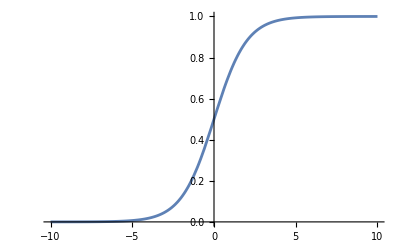

```mathematica
Plot[f=1/(1+Exp[-z]),{z,-10,10}]
```

```mathematica
z=2 r^2;
r=√(z/2);
```

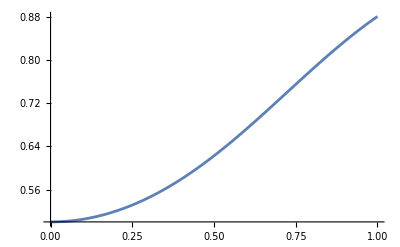

```mathematica
Plot[f=1/(1+Exp[-2 r^2]),{r,0,1}]
```

```mathematica
Plot[f=1/(1+Exp[-2 r^2]),{r,0,1}]
```